# Solving TOV equations.

#### Constants

```mathematica
(* Universal constants*)
G = 6.6743 10^-8;
c = 2.99792458 10^10;

(* Astronomical parameters*)
Subscript[M, Earth]=5.9724*^27;
Subscript[R, Earth] = 6.371*^8;
Subscript[M, Jupiter]=1.8982*^30;
Subscript[R, Jupiter]=6.991*^9;
Subscript[M, sun]= 1.9885*^33;
Subscript[R, sun]=6.957*^10;

α=G Subscript[M, sun]/(10^5 c^2);
Subscript[E0, sol]= Subscript[M, sun] c^2;

(* Nuclear parameters*)
mp=1.67262192369 10^-24;
mn=1.67492749804 10^-24;
me = 9.1093837015  10^-28;
λp=2.10308910336 10^-14;
λn =2.1001941552  10^-14;
λe = 3.8615926796  10^-11;

km = 10.0^5;
km3 = (10.0^5)^3;
rmin = 0.001;
rmax = 350;
densup = 7.860;
```

## 1 Equations of state:

## 1.1 Equation of state 1: Free gas of neutrons

#### 1.1.1 Relativistic Case (pure NS)

Let’s try first just this one: relativistic case

```mathematica
Pressure R[ϵ_]:=ϵ/3;
Density R[p_]:=3p;
```

#### 1.1.2 Non Relativistic Case (pure NS)

Pressure and density take the following form

```mathematica
ϵ(P) = 5 (m/(15 π^2 λ^3))^(2/5)P^(3/5)
```

with m, λ of the gas we are considering, let’s say neutrons only, then

```mathematica
kf[m_,l_]:=5((m c^2)/(15 π^2 l^3))^(0.4);
kn=kf[mn,λn];
kp=kf[mp,λp];
ke=kf[me,λe];

Density NR[p_]:=kn p^0.6
```

#### 1.1.3 Whole Range Neutron Star (Pure NS)

We need first to define density and pressure as function of non-dimensional fermi momentum

```mathematica
nfun[m_,l_]:= (m c^2)/(8 π^2 l^3)
epsilon i[z_,m_,l_]:= nfun[m,l]((2 z^3 + z )Sqrt[1 +z^2] - ArcSinh[z])
pressure i[z_,m_,l_]:=nfun[m,l]((2z^3 /3-z)Sqrt[1+z^2]+ArcSinh[z])
```

now, we create a table of data (p, ϵ):

```mathematica
ListEoS n={};
Do[ ListEoS n=Union[ListEoS n,Table[{pressure i[z,mn,λn],epsilon i[z,mn,λn]},{z,10.^i,10^(i+1)-10^(i-1),10^(i-2)}]],{i,-3,2}]
EoS n=Interpolation[ListEoS n,InterpolationOrder->1];
```

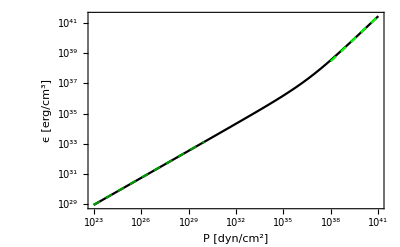

```mathematica
DNR=LogLogPlot[Density NR[x],{x,10^23, 10^30},
PlotStyle->{RGBColor[0.,0.6,0.],Dashed},
PlotLegends->Placed[{"Non Relativistic"},{Left,Top}]];
DR =LogLogPlot[Density R[x],{x,10^38, 10^41},
PlotStyle->{RGBColor[0.,1,0.], Dashed},
PlotLegends->Placed[{"Relativistic"},{Left,Top}]];
DNS=LogLogPlot[{EoS n[x]},{x,10^23,10^41},
Frame->True,
FrameLabel->{"P [dyn/cm^2]","ϵ [erg/cm^3]"},
PlotStyle->{ Black},
PlotLegends->Placed[{"Whole range"},{Left,Top}],
PlotTheme->"Scientific"];
Show[DNS,DNR, DR]
```

Now, let’s build the function for the whole range as a piecewise function taking the R and NR approx,

```mathematica
pw=Piecewise[{{Density NR[x], 0≤  x<10^23}, {EoS n[x],10^23≤ x≤ 10^45},{Density R[x],x>10^45}}];
dener n[p_]:=pw/.x-> p
```

Now we can proceed to do the numerical integration

## 1.2 Equation of state 2: Free gas of npe

```mathematica
Zp[z_,mn_,mp_,me_]:=Sqrt[(mn^2 (1+z^2) - (me^2 + mp^2))^2-4 mp^2 me^2 ]/(2 mp mn Sqrt[1 + z^2])
Ze[z_,mn_,mp_,me_]:=mp/me Zp[z,mn,mp,me]

epsilon pe[z_]:=  epsilon i[z,mp,λp]+epsilon i[mp/me z, me, λe]
pressure pe[z_]:=pressure i[z,mp,λp]+pressure i[mp/me z ,me,λe]

epsilon npe[z_]:= epsilon i[z,mn,λn]+ epsilon i[Zp[z,mn,mp,me],mp,λp]+epsilon i[mp/me Zp[z,mn,mp,me],me,λe]
pressure npe[z_]:=pressure i[z,mn,λn]+pressure i[Zp[z,mn,mp,me],mp,λp]+pressure i[mp/me Zp[z,mn,mp,me],me,λe]
```

Non relativistic regime (before z_critical=Zc)

```mathematica
Zc=Zp[0,mn,mp,me]
{pressure pe[Zc],pressure npe[0]}
```

0.0012654

{3.03851×10^24,3.03851×10^24}

```mathematica
ListEoS npe=Table[{pressure pe[z],epsilon pe[z]},{z,0,Zc,10^-6}];
Do[ ListEoS npe=Union[ListEoS npe,Table[{pressure npe[z],epsilon npe[z]},{z,10.^i,10^(i+1)-10^(i-1),10^(i-2)}]],{i,-3,2}]
dener npe=Interpolation[ListEoS npe,InterpolationOrder->1];
```

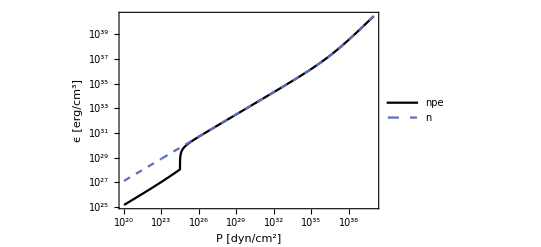

```mathematica
EquationOfState npe = LogLogPlot[{dener npe[x],dener n[x]},{x,10^20,10^40},
Frame->True,
FrameLabel->{"P [dyn/cm^2]","ϵ [erg/cm^3]"},
PlotStyle->{Black,Dashed},
PlotLegends->Placed[{"npe", "n"},{Left,Top}],
PlotTheme->"Scientific"]
```

```mathematica
Export["Plots/equation_of_state_npe_m.pdf",EquationOfState npe]
```

Plots/equation_of_state_npe_m.pdf

## 1.3 Equation of state 3: Interacting protons and neutrons

## 2. Hydrostatic Equilibrium equation

## 2.1 Newton Equations:

We solve first this simple case.

```mathematica
Pc = 3.3 10^34;
ListRG={};
Do[
Do[{
solutionN = NDSolve[{p'[r]== If[p[r]>0,-(α dener[p[r]*Pc]*M[r])/(Pc r^2),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],p[rmin]==1,M[rmin]==0.0},{p,M},{r,rmin,rad},MaxSteps->Infinity];
mass ad[x_]:=M[x]/.solutionN[[1]];
pressure ad[x_]:=p[x]/.solutionN[[1]];
If[pressure ad[rad]==0,
Print["Central Pressure = ", Pc, "\n",
	"Radius in km = ", rad, "\n",
	"Mass in M_s = ", mass ad[rad]];
Break[],
ListRG=Append[ListRG,{rad,dener[Pc*pressure ad[rad]]}]
];
},
{rad,1,25,.1}],{dener,{dener n,dener npe}}]
```

Central Pressure = 3.3×10^34
Radius in km = 14.8
Mass in M_s = 0.804716

Central Pressure = 3.3×10^34
Radius in km = 14.7
Mass in M_s = 0.797783

## 2.2 TOV equations and traversal time

### 2.2.1 Theory

The equations to solve are, in non dimensional form

```mathematica
(d p)/(d r)= -(α [M(r) + β(Pc) r^3 p(r)][ϵ(p(r)) + p(r)][r^2 - 2 α r M(r)])^-1
```

This gives us non dimensional pressure and energy density. Along with the non-dimensional mass, this will be useful to define the metric tensor component functions:

```mathematica
Subscript[g, rr](r)=A(r) = (1 - (2 G M(r))/r)^-1 = (1 - 2α (M̄)/r)^-1
```

with M̄ in units of solar masses and r in km. And the other function comes from the diff. eq.

```mathematica
(B'(r))/(B(r))= - (2 P'(r))/(P(r)+ϵ(r))
```

with boundary conditions in the surface equal to the Schwarzschild solution for the exterior metric.
Given  A=g_rr and B=g_tt, we already have all the components of the metric. The general energy diff. eq. is

```mathematica
1/2(dr/dτ)^2+1/2 g^rr(r)(1 - g^tt(r) E^2)c^2=0
```

from this energy-like equation, consider the potential part, at the turning points (r=R),

```mathematica
V(R) = 1/2 g^rr(R)(1 - g^tt(R) E^2)c^2=0
E^2= 1/(g^tt(R))= Subscript[g, tt](R) 
-> E^2 = B(R)
```

we have therefore the following integral:

```mathematica
Δτ = 2/c∫(√(-Subscript[g, tt](r)))/(√(1 - E^2/Subscript[g, rr](r)))ⅆr
Δτ = 2/c(∫_0)^R(√(A(r)B(r)))/(√(B(R)- B(r)))ⅆr
```

that gives us proper times in seconds.

### 2.2.2 Numerical Computation

The following is the code that returns proper times for some NS’s with different central pressures:

```mathematica
ListPc ={ 10.^32, 10.^35, 10.^36, 10.^37, 10.^38, 10.^39, 10.^40};
Do[{
Pc = ListPc[[ñ]];

Print["NS ", ñ, " - Central Pressure: ", ScientificForm[Pc]]; 

Do[{
Listϵ={};
Listp={};

Do[{

(* TOV eqs*)
solutionTOV = NDSolve[
{p'[r]== If[p[r]>0,-α*(M[r]+(4 π (Pc km3)/Subscript[E0, sol])r^3 p[r] )(dener[p[r]*Pc]/Pc+p[r])/(r(r - 2 α  M[r])),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],
p[rmin]==1.0,M[rmin]==0.0},{p,M},{r,rmin,rad},MaxSteps->Infinity];
(**** Interpolation of solutions****)
mass[x_]=M[x]/.solutionTOV[[1]];
TOVpressure[x_]:=p[x]/.solutionTOV[[1]];

(**** Integrate until surface ****)
If[TOVpressure[rad]==0,
Break[],
Listϵ=Append[Listϵ,{rad,dener[Pc*TOVpressure[rad]]/Pc}];
Listp=Append[Listp,{rad,TOVpressure[rad]}];
R=rad;
MStar=mass[rad];
];
},{rad,rmin+0.1,25,.1}];

Print["R (km) = ", R, "\n",
	"M  (M_s)  ", MStar, "\n",
	"R̂     =  ", Rhat[R km, MStar*Subscript[M, sun]]],


ϵ n= Interpolation[Listϵ,InterpolationOrder->10];
p n =Interpolation[Listp,InterpolationOrder->10];

(**** Metric coefficients ****)

A[r_]:= (1 - 2 α mass[r]/r)^-1;

Bmax =1- (2 α)/R;
BFunction=NDSolve[ {Bb'[r] == -2 Bb[r] p n'[r]/(p n[r]+ϵ n[r]),Bb[R]== Bmax},Bb[r],{r,rmin+0.1,R}];
B[r_]=Bb[r]/.BFunction[[1]];

(****Computing times ****)

τsNS =2 NIntegrate[Sqrt[A[r] B[r]/(B[R]-B[r])],{r,rmin,R}]/(10^(-5) c);
tsNS =2 NIntegrate[Sqrt[A[r] B[R]/(B[r](B[R]-B[r]))],{r,rmin,R}]/(10^(-5) c);

Print["τ (min): ", τsNS/60,"\n",
	"t  (min): ", tsNS/60, "\n",
	"τs (min): ", τ[Rhat[R km, MStar*Subscript[M, sun]]]/ω[R km, MStar*Subscript[M, sun]]/60,"\n",
	"ts (min): ", t[Rhat[R km, MStar*Subscript[M, sun]]]/ω[R km, MStar*Subscript[M, sun]]/60,"\n",
"----------------------------------------"]},{dener,{dener n, dener npe}}]
},{ñ,1,Length[ListPc]}]
```

NS 1 - Central Pressure: 1.×10^32

R (km) = 24.901
M  (M_s)  0.15762
R̂     =  0.0966812

τ (min): 0.0000369392
t  (min): 0.0000396606
τs (min): 0.0000447447
ts (min): 0.0000453838
----------------------------------------

R (km) = 24.901
M  (M_s)  0.157267
R̂     =  0.096573

τ (min): 0.0000369609
t  (min): 0.0000396835
τs (min): 0.0000447954
ts (min): 0.0000454338
----------------------------------------

NS 2 - Central Pressure: 1.×10^35

R (km) = 11.301
M  (M_s)  0.675455
R̂     =  0.297088

τ (min): 5.04996×10^-6
t  (min): 6.52236×10^-6
τs (min): 6.28129×10^-6
ts (min): 7.29025×10^-6
----------------------------------------

R (km) = 11.301
M  (M_s)  0.667139
R̂     =  0.295253

τ (min): 4.97673×10^-6
t  (min): 6.4344×10^-6
τs (min): 6.32526×10^-6
ts (min): 7.32612×10^-6
----------------------------------------

NS 3 - Central Pressure: 1.×10^36

R (km) = 7.601
M  (M_s)  0.688626
R̂     =  0.365764

τ (min): 2.63357×10^-6
t  (min): 4.12453×10^-6
τs (min): 3.31229×10^-6
ts (min): 4.22073×10^-6
----------------------------------------

R (km) = 7.601
M  (M_s)  0.674548
R̂     =  0.362006

τ (min): 2.66526×10^-6
t  (min): 4.15605×10^-6
τs (min): 3.35433×10^-6
ts (min): 4.24864×10^-6
----------------------------------------

NS 4 - Central Pressure: 1.×10^37

R (km) = 5.301
M  (M_s)  0.525259
R̂     =  0.382519

τ (min): 1.6918×10^-6
t  (min): 3.43382×10^-6
τs (min): 2.18522×10^-6
ts (min): 2.86461×10^-6
----------------------------------------

R (km) = 5.301
M  (M_s)  0.512262
R̂     =  0.377757

τ (min): 1.74547×10^-6
t  (min): 3.49567×10^-6
τs (min): 2.21976×10^-6
ts (min): 2.88579×10^-6
----------------------------------------

NS 5 - Central Pressure: 1.×10^38

R (km) = 5.101
M  (M_s)  0.37901
R̂     =  0.33124

τ (min): 1.87396×10^-6
t  (min): 3.84259×10^-6
τs (min): 2.50253×10^-6
ts (min): 3.03004×10^-6
----------------------------------------

R (km) = 5.101
M  (M_s)  0.368442
R̂     =  0.326589

τ (min): 1.73861×10^-6
t  (min): 3.61202×10^-6
τs (min): 2.54414×10^-6
ts (min): 3.06135×10^-6
----------------------------------------

NS 6 - Central Pressure: 1.×10^39

R (km) = 6.501
M  (M_s)  0.407265
R̂     =  0.304154

τ (min): 2.6389×10^-6
t  (min): 4.54486×10^-6
τs (min): 3.51856×10^-6
ts (min): 4.11718×10^-6
----------------------------------------

R (km) = 6.501
M  (M_s)  0.395745
R̂     =  0.299821

τ (min): 2.43886×10^-6
t  (min): 4.24879×10^-6
τs (min): 3.57621×10^-6
ts (min): 4.16362×10^-6
----------------------------------------

NS 7 - Central Pressure: 1.×10^40

R (km) = 6.201
M  (M_s)  0.440884
R̂     =  0.324023

τ (min): 2.3859×10^-6
t  (min): 4.32341×10^-6
τs (min): 3.12123×10^-6
ts (min): 3.74315×10^-6
----------------------------------------

R (km) = 6.301
M  (M_s)  0.430569
R̂     =  0.317659

τ (min): 2.1535×10^-6
t  (min): 3.96014×10^-6
τs (min): 3.24509×10^-6
ts (min): 3.86011×10^-6
----------------------------------------

```mathematica
PureNSDensity=ListLogPlot[Listϵ,Joined->True,
Frame->True,
PlotStyle->Red,
FrameLabel->{"r [km]","ρ(r) [g / cm^3]"}]
```

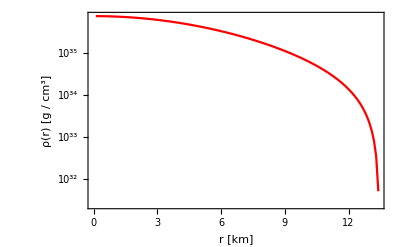

```mathematica
Export["Plots/PureNS_Density.pdf",PureNSDensity];
```

Schwarzschild times

```mathematica
Rhat[R_, M_]:= Sqrt[(G M)/(c^2 R)]
Em[R_]:=√(1-2 R^2)
x[r_,R_]:= Sqrt[1-2r^2]/Sqrt[1-2 R^2]
ω [R_,M_] :=Sqrt[ (G M)/R^3]
τ[R_]:=2 Re[NIntegrate[1/(x[r,R] Em[R])(3-x[r,R])/Sqrt[(5-x[r,R])(x[r,R]-1)],{r,0,R},WorkingPrecision->10, AccuracyGoal->20]]

t[R_]:= 2 NIntegrate[Re[4/(Em[R]^2x[r,R](3-x[r,R])Sqrt[(5 - x[r,R])(x[r,R]-1)] )],{r,0,R},WorkingPrecision->10, AccuracyGoal->20]
```

```mathematica
Do[{Pc=3.408 10^35;
dener=dener npe;
(* TOV eqs*)
solutionTOV = NDSolve[
{p'[r]== If[p[r]>0,-α*(M[r]+(4 π (Pc km3)/Subscript[E0, sol])r^3 p[r] )(dener[p[r]*Pc]/Pc+p[r])/(r(r - 2 α  M[r])),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],
p[rmin]==1.0,M[rmin]==0.0},{p,M},{r,rmin,rad},MaxSteps->Infinity];
(**** Interpolation of solutions****)
mass[x_]=M[x]/.solutionTOV[[1]];
TOVpressure[x_]:=p[x]/.solutionTOV[[1]];

Print[rad, "\t", mass[rad], "\t", TOVpressure[rad]];
(**** Integrate until surface ****)
If[TOVpressure[rad]==0,
Break[],
R=rad;
MStar=mass[rad];
];
},{rad,5,30,1}]
```

5	0.44785	0.0961367

6	0.565118	0.0344425

7	0.644756	0.0094012

8	0.686599	0.00147428

9	0.698866	0.0000172938

10	0.699075	0.